Emaad Khwaja - Interpolation - Math 385 - 03/21/16

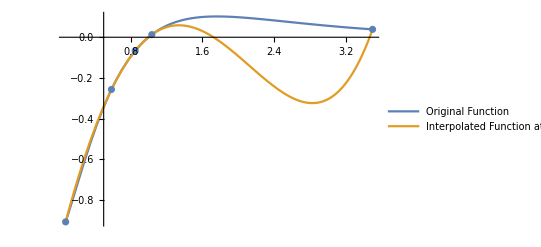

Norm Interpolation Error = 0.112275

```mathematica
nb=EvaluationNotebook[];
NotebookFind[nb,"5",All,CellTags];

NumberofPoints= 5;
n1=NumberofPoints;
n=n1;
f[x_]:=x^(E^-x)-1
RandomPoints=RandomSample[DeleteCases[RandomReal[n,n],0],n];
V1=Partition[Riffle[RandomPoints,f[RandomPoints]],2];
V=V1;
A=IdentityMatrix[n]-IdentityMatrix[n];
b=RandomSample[Range[n],n];
xs=RandomSample[Range[n],n];
r=Range[(n)]-1;

For[i=0,i<n, i++
For[j=0,j<n,j++
If[i≥0,A[[j,i]]=V[[j,1]]^(i-1)]
]
];

If[Abs[Det[A]]>10^-6,
For[j=0,j<n, j++
If[j≥0,b[[j]]=V[[j,2]]]
];

For[j=0,j<n, j++
If[j≥0,xs[[j]]=V[[j,1]]]
];

a=N[LinearSolve[A,b]];

q=Sum[a[[i]]*(V[[i,1]]^r[[i]]),{i,1,n}];

g[x_]=Sum[a[[i]]*(x^r[[i]]),{i,1,n}];

Show[Plot[{f[x],g[x]},{x,Min[xs],Max[xs]},PlotLegends->LineLegend[{"Original Function","Interpolated Function at 5 points"}]],ListPlot[V]],SelectionEvaluate[nb]]

error1=1/(Max[xs]-Min[xs])*((NIntegrate[(f[x]-g[x])^2,{x,Min[xs],Max[xs]}])^(1/2));

Print["Norm Interpolation Error = ", error1]
```

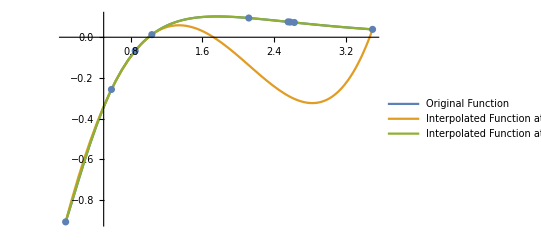

Norm Interpolation Error = 0.046641

Is the norm interpolation error smaller after using more points? True

```mathematica
ncEvaluationNotebook[];
NotebookFind[nc,"10",All,CellTags];
AdditionalPoints= 8;
n2=AdditionalPoints;
n=n1+n2;
RandomPoints2=RandomSample[DeleteCases[DeleteCases[RandomReal[n2,n2],0],RandomPoints],n2];
V2=Partition[Riffle[RandomPoints2,f[RandomPoints2]],2];
A=IdentityMatrix[n]-IdentityMatrix[n];
V=Join[V1,V2];
xs2=RandomSample[Range[n],n];
b=RandomSample[Range[n],n];
r=Range[(n)]-1;

For[i=0,i<n, i++
For[j=0,j<n,j++
If[i≥0,A[[j,i]]=V[[j,1]]^(i-1)]
]
];


If[Abs[Det[A]]>(10^-6),
For[j=0,j<n, j++
If[j≥0,b[[j]]=V[[j,2]]]
];

For[j=0,j<n, j++
If[j≥0,xs2[[j]]=V[[j,1]]]
];

a=N[LinearSolve[A,b]];

q=Sum[a[[i]]*(V[[i,1]]^r[[i]]),{i,1,n}];

h[x_]=Sum[a[[i]]*(x^r[[i]]),{i,1,n}];

Show[Plot[{f[x],g[x],h[x]},{x,Min[xs],Max[xs]},PlotLegends->LineLegend[{"Original Function","Interpolated Function at 5 points","Interpolated Function at 10 points"}]],ListPlot[V]],SelectionEvaluate[nc]]

error2=1/(Max[xs2]-Min[xs2])*((NIntegrate[(f[x]-h[x])^2,{x,Min[xs2],Max[xs2]}])^(1/2));

Print["Norm Interpolation Error = ", error2]

Print["Is the norm interpolation error smaller after using more points? ", error2<error1]

Off[LinearSolve::luc]
```